Schakenberg system

```mathematica
Consider the Schnakenberg system:

-Graphics--Graphics--Graphics-

Let u be the activator and v be the inhibitor.

(∂u(x,t))/(∂t) = D (∂^2 u(x,t))/(∂x^2)+γ (a-u+u^2 v)

(∂v(x,t))/(∂t) =d D (∂^2 v(x,t))/(∂x^2)+γ (b-u^2 v)
```

Define the reaction functions

```mathematica
f[u_,v_]=a-u+u^2*v
g[u_,v_]=b-u^2*v
```

a-u+u^2 v

b-u^2 v

```mathematica
{{us,vs}}={u,v}/.Solve[{f[u,v]==0,g[u,v]==0},{u,v}]
```

{{a+b,b/(a+b)^2}}

```mathematica
fu=D[f[u,v],u]/.{u->us,v->vs}//FullSimplify
```

-1+(2 b)/(a+b)

```mathematica
fv=D[f[u,v],v]/.{u->us,v->vs}//Simplify
```

(a+b)^2

```mathematica
gu=D[g[u,v],u]/.{u->us,v->vs}//Simplify
```

-(2 b)/(a+b)

```mathematica
gv=D[g[u,v],v]/.{u->us,v->vs}//Simplify
```

-(a+b)^2

```mathematica
detA=fu*gv-fv*gu//FullSimplify
```

(a+b)^2

Next determine the range of a,b that are possible for the Turing instability.

```mathematica
trA=(fu+gv)//FullSimplify
```

-1+(2 b)/(a+b)-(a+b)^2

```mathematica
R1[a_,b_]=(a+b)^3-(b-a)
```

a-b+(a+b)^3

```mathematica
Solve[{{R1[a,b]/.{a->0}}==0,b>0},b]
```

{{b→1}}

```mathematica
(* so b should be bigger than 1 *)
```

```mathematica
R2[a_,b_,d_]=d*(b-a)-(a+b)^3
```

-(a+b)^3+(-a+b) d

```mathematica
d/.Solve[{{R2[a,b,d]/.{a->0}}==0},d]
```

{b^2}

```mathematica
(* so d should be bigger than b^2 *)
```

## Next look at the critical diffusion coefficients for the Turing instability

```mathematica
Md[d_]=(d*fu+gv)^2-4*d*detA//FullSimplify
```

(-4 (a+b)^4 d+((a+b)^3+(a-b) d)^2)/(a+b)^2

```mathematica
{d1,d2}={d}/.Solve[Md[d]==0,d]//FullSimplify
```

{{(a+b)^6/(2 √2 √(b (a+b)^7)+(a+b)^3 (a+3 b))},{(a+b)^6/(-2 √2 √(b (a+b)^7)+(a+b)^3 (a+3 b))}}

```mathematica
dc=d1/.{a->0,b->2}
dc2=d2/.{a->0,b->2}
```

{64/(48+32 √2)}

{64/(48-32 √2)}

```mathematica
N[dc]
N[dc2]
```

{0.686292}

{23.3137}

So the critical ratio of diffusion coefficients is approx 23.

```mathematica
Range of unstable wavenumbers
Recall that m=π l^2
```

of Range unstable wavenumbers

Set::write: Tag Times in m Recall that is Protected.

l^2

```mathematica
h[m_]=d*m^2-g*(d*fu+gv)*m+g^2*detA//FullSimplify
```

(a+b)^2 g^2+(((a+b)^3+(a-b) d) g m)/(a+b)+d m^2

```mathematica
hh[m]=h[m]/.{d->1.1*dc2,a->0,b->2}
```

{4 g^2-21.6451 g m+25.6451 m^2}

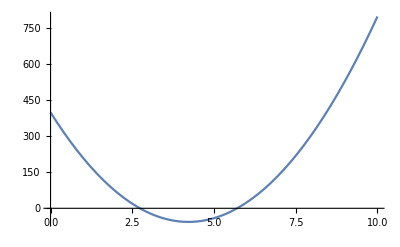

```mathematica
Plot[hh[m]/.{g->10},{m,0,10}]
```

```mathematica
{m1,m2}={m}/.Solve[{hh[m]}==0,m]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.273288 g},{0.570737 g}}

```mathematica
m1/.{g->10}
```

{2.73288}

```mathematica
m2/.{g->10}
```

{5.70737}

```mathematica
Sqrt[.27*g]/Pi
```

0.165399 √g

```mathematica
Sqrt[.57*g]/Pi
```

0.240319 √g

```mathematica
lambdap[m_]=-(m*(1+d)-g*(fu+gv))+Sqrt[(m*(1+d)-g*(fu+gv))^2-4*h[m]]
```

(-1+(2 b)/(a+b)-(a+b)^2) g-(1+d) m+√((-(-1+(2 b)/(a+b)-(a+b)^2) g+(1+d) m)^2-4 ((a+b)^2 g^2+(((a+b)^3+(a-b) d) g m)/(a+b)+d m^2))

```mathematica
Llambdap[m]=lambdap[m]/.{d->1.1*dc2,a->0,b->2}
```

{-3 g-26.6451 m+√((3 g+26.6451 m)^2-4 (4 g^2-21.6451 g m+25.6451 m^2))}

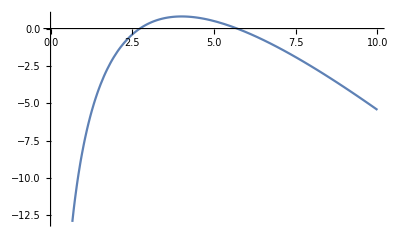

```mathematica
Plot[Re[{Llambdap[m]/.{g->10}}],{m,0,10}]
```

```mathematica
lambdam[m_]=-(m*(1+d)-g*(fu+gv))-Sqrt[(m*(1+d)-g*(fu+gv))^2-4*h[m]]//FullSimplify
```

(-1+(2 b)/(a+b)-(a+b)^2) g-(1+d) m-√((((a-b+(a+b)^3) g+(a+b) (1+d) m)^2-4 (a+b) ((a+b)^3 g^2+((a+b)^3+(a-b) d) g m+(a+b) d m^2))/(a+b)^2)

```mathematica
Llambdam[m]=lambdam[m]/.{d->1.1*dc2,a->0,b->2}
```

{-3 g-26.6451 m-1/2 √((6 g+53.2902 m)^2-8 (8 g^2-43.2902 g m+51.2902 m^2))}

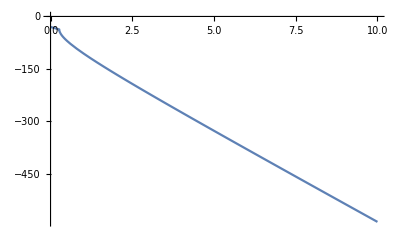

```mathematica
Plot[Re[{Llambdam[m]/.{g->10}}],{m,0,10}]
```

```mathematica
Now, lets go back and figure out what controls the range of unstable wavenumbers.
```

```mathematica
{mm1,mm2}={m}/.Solve[{h[m]}==0,m]//FullSimplify
```

{{-(a^3 g+3 a^2 b g+3 a b^2 g+b^3 g+a d g-b d g+(a+b) √((((a+b)^6-2 (a+b)^3 (a+3 b) d+(a-b)^2 d^2) g^2)/(a+b)^2))/(2 (a+b) d)},{-(a^3 g+3 a^2 b g+3 a b^2 g+b^3 g+a d g-b d g-(a+b) √((((a+b)^6-2 (a+b)^3 (a+3 b) d+(a-b)^2 d^2) g^2)/(a+b)^2))/(2 (a+b) d)}}

```mathematica
r1=mm1
```

{-(a^3 g+3 a^2 b g+3 a b^2 g+b^3 g+a d g-b d g+(a+b) √((((a+b)^6-2 (a+b)^3 (a+3 b) d+(a-b)^2 d^2) g^2)/(a+b)^2))/(2 (a+b) d)}

```mathematica
r2=mm2
```

{-(a^3 g+3 a^2 b g+3 a b^2 g+b^3 g+a d g-b d g-(a+b) √((((a+b)^6-2 (a+b)^3 (a+3 b) d+(a-b)^2 d^2) g^2)/(a+b)^2))/(2 (a+b) d)}

```mathematica
r=r2-r1//FullSimplify
```

{(√((((a+b)^6-2 (a+b)^3 (a+3 b) d+(a-b)^2 d^2) g^2)/(a+b)^2))/d}

```mathematica
(* so as d gets big, this tends to (a-b)/(a+b)g *)
```

```mathematica
r/.{a->0,b->2,g->1}//FullSimplify
```

{(√(16+(-24+d) d))/d}

```mathematica
r1//.{a->0,b->2,g->1}//FullSimplify
```

{(-4+d-√(16+(-24+d) d))/(2 d)}

```mathematica
r2//.{a->0,b->2,g->1}//FullSimplify
```

{(-4+d+√(16+(-24+d) d))/(2 d)}

```mathematica
N[r1/.{d->1000*dc2,a->0,b->2,g->1}]
```

{{0.000171632}}

```mathematica
N[r2/.{d->1000*dc2,a->0,b->2,g->1}]
```

{{0.999657}}

```mathematica
mMax=m/.Solve[D[h[m],m]==0,m]
```

{-((a^3+3 a^2 b+3 a b^2+b^3+a d-b d) g)/(2 (a+b) d)}

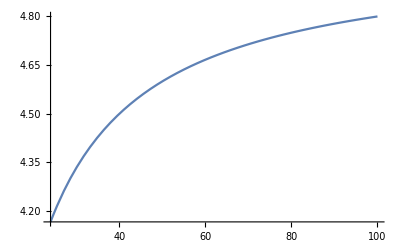

```mathematica
Plot[mMax/.{g->10,a->0,b->2},{d,24,100}]
```

```mathematica
mmMax=mMax/.{a->0,b->2,d->1.1*dc2}
```

{{0.422012 g}}

```mathematica
(* So, the fastest growing mode, when g=10, is given by *)
l=Sqrt[.42*g]/Pi/.{g->100}
```

2.06288

```mathematica
(* 

This means that no modes will grow in the simulation since l≥1 in practice. Next, let's choose g to make a specific mode the maximum growing mode.

*)
```

```mathematica
gmax[lmax_]=(Pi*lmax)^2/.42
```

23.4991 lmax^2

```mathematica
gmax[3]
```

211.492